## Notes on 2010 problem 3a integral.

We see that Cos + Sin looks like a scaled shifted sine or cosine with the same 2 Pi period

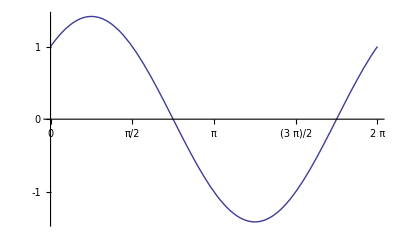

```mathematica
Plot[Cos[t]+Sin[t], {t, 0, 2 Pi}, Ticks -> {{0, Pi/2, Pi, 3 Pi/2, 2 Pi}, {-1, 0, 1}}]
```

and we can show that this sum can be written as

```mathematica
FullSimplify[Sqrt[2] Cos[t - Pi/4]]
FullSimplify[Sqrt[2] Cos[t + Pi/4]]
```

Cos[t]+Sin[t]

Cos[t]-Sin[t]

So our integral takes the form

```mathematica
Clear[a, b, c]
Integrate[w E^(I  b w(Cos[t] )), {w, 0, a}, {t, 0, 2 Pi}]
Integrate[w E^(I   w(b Cos[t] + c Sin[t])), {w, 0, a}, {t, 0, 2 Pi}]
Plot[{Sinc[x], BesselJ[1, -x]/(-x)}, {x, -4 Pi, 4 Pi}]
```

(2 a π BesselJ[1,a b])/b

```mathematica
a^2 π Hypergeometric0F1Regularized[2,-1/4 a^2 (b^2+c^2)] // TraditionalForm
 Manipulate[Plot[ x^2 Hypergeometric0F1Regularized[2,- arg x^2/4]
, {x, -4 Pi, 4 Pi}
, PlotRange->Full
, AxesLabel->{x, x^2 Hypergeometric0F1Regularized[2,- arg x^2/4]}
] , { {arg, 0.0001}, 0.01, 1} ]
```

π a^2 2-1/4 a^2 (b^2+c^2)

```mathematica
π a^2 2-1/4 a^2 (b^2+c^2) /. a -> R
```

```mathematica
π R^2 Hypergeometric0F1Regularized[2,-1/4 (b^2+c^2) R^2] /. b -> -k α
```

```mathematica
π R^2 Hypergeometric0F1Regularized[2,-1/4 R^2 (c^2+k^2 α^2)] /. c -> -k β
```

```mathematica
π R^2 Hypergeometric0F1Regularized[2,-1/4 R^2 (k^2 α^2+k^2 β^2)] // Simplify
```

```mathematica
π R^2 Hypergeometric0F1Regularized[2,-1/4 k^2 R^2 (α^2+β^2)] // TraditionalForm
```

π R^2 2-1/4 k^2 R^2 (α^2+β^2)